```mathematica
lst=Table[0,8,61];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
```

General::munfl: 8.59599×10^-302 8.71427×10^-17 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.32866×10^-292 (-8.53545×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.59599×10^-302 (-8.53545×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
lst
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\16082023_corr_modified\\corr_ana_ma.dat",lst,"Table"];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},Joined->True]]
```

-Graphics-

```mathematica
Export["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\corr_ana.dat",lst]
corr0=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_0.dat",Number];
corr1=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_1.dat",Number];
corr2=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_2.dat",Number];
corr3=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_3.dat",Number];
corr4=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_4.dat",Number];
corr5=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_5.dat",Number];
corr6=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_6.dat",Number];
corr7=ReadList["F:\\ThesisProject\\RESULTS\\19052023_corr_ana_h7\\corr_s_7.dat",Number];
```

F:\ThesisProject\RESULTS\26052023_corr_modified\corr_ana.dat

```mathematica
plst=Table[0,{i,8},{j,31},{k,2}];
For[i=0,i<8,i++,plst[[i+1]]=Transpose[{Table[i,{i,-30,30}],lst[[i+1]]}]];
```

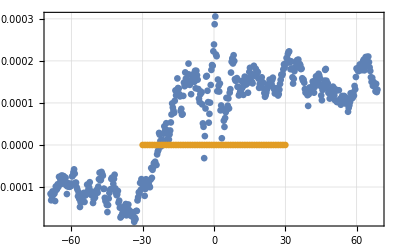

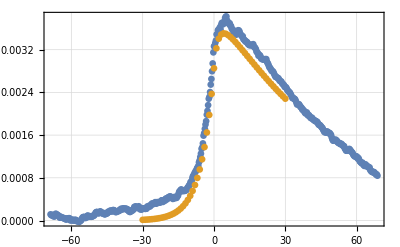

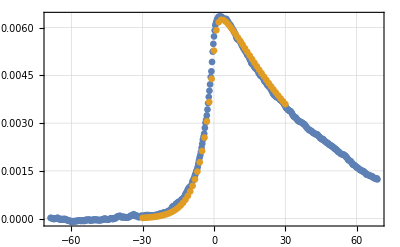

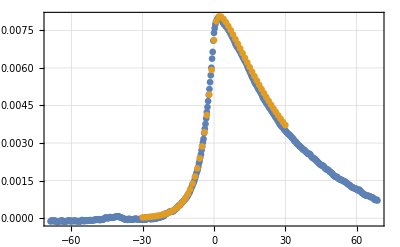

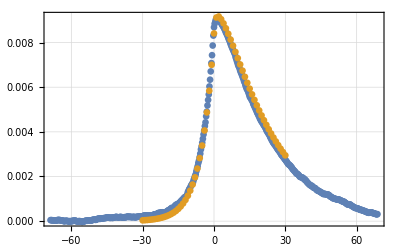

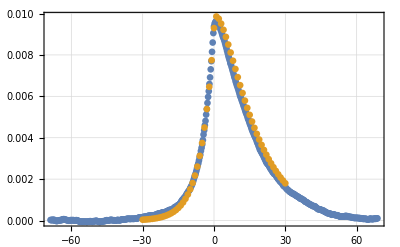

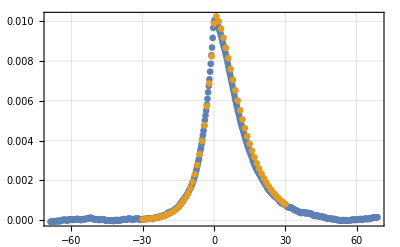

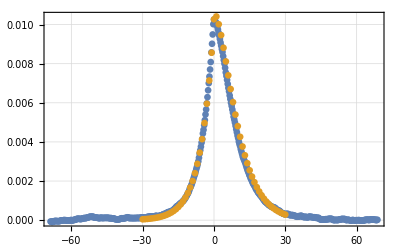

```mathematica
scalF=5.5;
pcr0=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr0}];

ListPlot[{pcr0,plst[[1]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr1=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr1}];

ListPlot[{pcr1,plst[[2]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr2=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr2}];

ListPlot[{pcr2,plst[[3]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr3=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr3}];

ListPlot[{pcr3,plst[[4]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr4=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr4}];

ListPlot[{pcr4,plst[[5]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr5=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr5}];

ListPlot[{pcr5,plst[[6]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr6=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr6}];

ListPlot[{pcr6,plst[[7]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
pcr7=Transpose[{Table[i,{i,-12.5*scalF,12.5*scalF,0.05*scalF}],corr7}];

ListPlot[{pcr7,plst[[8]]},PlotStyle->PointSize[0.012],PlotTheme->"Detailed",PlotRange->All,DataRange->{-30.30}]
```

```mathematica
(**)
```

```mathematica
dlst=Table[0,8,31];
For[gg=0,gg<8,gg++,dlst[[gg+1]]=Table[lst[[gg+1,31-i]]-lst[[gg+1,31+i]],{i,-30,0}]];
```

```mathematica
Rasterize[ListPlot[dlst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,0},Joined->True]]
Export["F:\\ThesisProject\\RESULTS\\26052023_corr_modified\\DCtau_eq.dat",dlst];
```

-Graphics-

```mathematica
(*24.05.2023*)
```

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"];
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

```mathematica
Rasterize[ListPlot[maxc,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},Joined->True]]
```

-Graphics-

```mathematica
Rasterize[ListPlot[maxt,PlotLegends->Table[i,{i,1,13,3}],DataRange->{0,10},PlotRange->All,Joined->True]]
```

-Graphics-

```mathematica
(*25.05.2023*)
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat",lst]
```

F:\ThesisProject\RESULTS\25052023_extrema\h10.dat

```mathematica
ilst=Import["F:\\ThesisProject\\RESULTS\\25052023_extrema\\h10.dat","Table"];
```

```mathematica
ilst[[1]]={0,Infinity};
```

```mathematica
fitMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,1]]}];
fitTMax=Transpose[{Table[i,{i,0,12,0.5}],ilst[[All,2]]}];
```

FittedModel[-0.0000219197+0.00102339 x-0.00016372 x^2+0.0000119369 x^3-3.28706×10^-7 x^4]

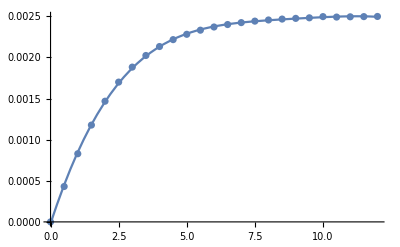

```mathematica
nlm=NonlinearModelFit[fitMax,a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
Show[ListPlot[ilst[[All,1]],DataRange->{0,12},PlotRange->All],Plot[nlm[x],{x,0,12}]]
```

FittedModel[18.7195-1.50103/x-4.71804 x+0.371601 x^2-0.00456264 x^3-0.000364738 x^4]

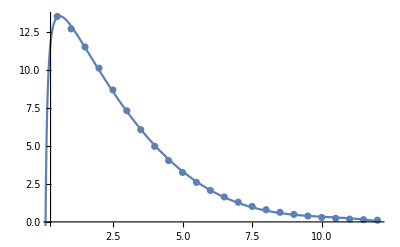

```mathematica
nlmt=NonlinearModelFit[fitTMax[[2;;25]],a+b x+c x^2+d x^3+e x^4+f x^(-1),{a,b,c,d,e,f},x]
Show[ListPlot[ilst[[All,2]],DataRange->{0,12},PlotRange->All],Plot[nlmt[x],{x,0,12}]]
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\25052023_extrema\\fit.dat",{nlm//Normal,nlmt//Normal}]
```

F:\ThesisProject\RESULTS\25052023_extrema\fit.dat

```mathematica
max1=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h1.txt"],"Data"];
max4=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h4.txt"],"Data"];
max7=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h7.txt"],"Data"];
max10=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h10.txt"],"Data"];
max13=ImportString[Import["F:\\ThesisProject\\RESULTS\\24052023_extrema\\h13.txt"],"Data"];
maxc={max1[[All,1]],max4[[All,1]],max7[[All,1]],max10[[All,1]],max13[[All,1]]};
maxc[[All,1]]=Table[0,5];
maxc//MatrixForm
maxt={max1[[All,2]],max4[[All,2]],max7[[All,2]],max10[[All,2]],max13[[All,2]]};
maxt[[All,1]]=Table[0,5];
maxt//MatrixForm
```

(0 | 0.0562453 | 0.0887259 | 0.102058 | 0.107213 | 0.10916
0 | 0.0233935 | 0.0353066 | 0.0400117 | 0.0418152 | 0.0424933
0 | 0.00625079 | 0.0091827 | 0.0102691 | 0.0106702 | 0.0108184
0 | 0.0014678 | 0.00213307 | 0.0023707 | 0.00245623 | 0.00248632
0 | 0.000332398 | 0.000481201 | 0.000533496 | 0.000552089 | 0.000558832)

(0 | 0.269867 | 0.129315 | 0.052779 | 0.0202246 | 0.00755684
0 | 0.964786 | 0.476559 | 0.200015 | 0.0778965 | 0.0293205
0 | 3.3005 | 1.62697 | 0.679211 | 0.26338 | 0.0989795
0 | 10.101 | 4.96469 | 2.0674 | 0.800207 | 0.301444
0 | 28.5502 | 13.9992 | 5.81894 | 2.24996 | 0.843757)

{{38.3194,41.5955,43.0497,43.6496,43.9041},{15.9377,16.552,16.8776,17.0241,17.0908},{4.25861,4.30493,4.3317,4.34415,4.35119},{1.,1.,1.,1.,1.},{0.22646,0.225591,0.225038,0.224771,0.224763}}

FittedModel[-1.02185+44.2437/x]

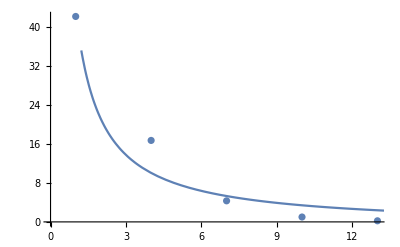

```mathematica
rate=Table[maxc[[i,2;;6]]/maxc[[4,2;;6]],{i,1,5}]
ratefit=Mean[Transpose[rate]];
ratefit=Transpose[{{1,4,7,10,13},ratefit}];
line=NonlinearModelFit[ratefit,a+b/x,{a,b,c,d},x]
Show[ListPlot[ratefit],Plot[line[x],{x,0,15}]]
```

{{0.0267168,0.0260469,0.0255292,0.0252742,0.0250688},{0.0955137,0.0959895,0.0967474,0.0973454,0.0972668},{0.326749,0.327708,0.328534,0.32914,0.328351},{1.,1.,1.,1.,1.},{2.82647,2.81974,2.81462,2.81173,2.79905}}

FittedModel[-0.0305447+0.0338354 ⅇ^(0.340939 x)]

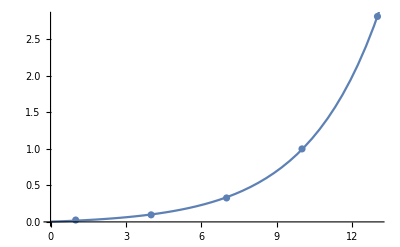

```mathematica
ratet=Table[maxt[[i,2;;6]]/maxt[[4,2;;6]],{i,1,5}]
ratetfit=Mean[Transpose[ratet]];
ratetfit=Transpose[{{1,4,7,10,13},ratetfit}];
linet=NonlinearModelFit[ratetfit,a+b Exp[c x],{a,b,c,d},x]
Show[ListPlot[ratetfit],Plot[linet[x],{x,0,15}]]
```

```mathematica
lmtM0=Limit[matJump,g->0]
eigVa0=Eigenvalues[lmtM0]
eigVeR0=Eigenvectors[lmtM0]
eigVeL0=Eigenvectors[Transpose[lmtM0]];
eigNVeL0=Table[eigVeL0[[i]]/(eigVeL0[[i]].eigVeR0[[i]]),{i,1,8}]
nessDist0=Limit[nessDist,g->0]
```

{{-3 ⅇ^(h/4),ⅇ^(-h/4),ⅇ^(-h/4),0,ⅇ^(h/4),0,0,0},{ⅇ^(h/4),-3 ⅇ^(-h/4),0,ⅇ^(-3 h/4),0,ⅇ^(-h/4),0,0},{ⅇ^(h/4),0,-3 ⅇ^(-h/4),ⅇ^(-3 h/4),0,0,ⅇ^(-h/4),0},{0,ⅇ^(-h/4),ⅇ^(-h/4),-3 ⅇ^(-3 h/4),0,0,0,ⅇ^(-3 h/4)},{ⅇ^(h/4),0,0,0,-3 ⅇ^(h/4),ⅇ^(-h/4),ⅇ^(-h/4),0},{0,ⅇ^(-h/4),0,0,ⅇ^(h/4),-3 ⅇ^(-h/4),0,ⅇ^(-3 h/4)},{0,0,ⅇ^(-h/4),0,ⅇ^(h/4),0,-3 ⅇ^(-h/4),ⅇ^(-3 h/4)},{0,0,0,ⅇ^(-3 h/4),0,ⅇ^(-h/4),ⅇ^(-h/4),-3 ⅇ^(-3 h/4)}}

{0,-4 ⅇ^(-h/4),-2 ⅇ^(-h/4),ⅇ^(-3 h/4) (-1-ⅇ^(h/2)-ⅇ^h-√(1-ⅇ^h+ⅇ^(2 h))),ⅇ^(-3 h/4) (-1-ⅇ^(h/2)-ⅇ^h+√(1-ⅇ^h+ⅇ^(2 h))),ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,1],ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,2],ⅇ^(-3 h/4) Root[48 ⅇ^(3 h/2)+(14 ⅇ^(h/2)+16 ⅇ^h+14 ⅇ^(3 h/2)) #1+(4+4 ⅇ^(h/2)+4 ⅇ^h) #1^2+#1^3&,3]}

{{ⅇ^-h,ⅇ^(-h/2),ⅇ^(-h/2),1,ⅇ^-h,ⅇ^(-h/2),ⅇ^(-h/2),1},6,{(ⅇ^(-3 h/2) (48 ⅇ^(2 h)+28 ⅇ^h Root[48 ⅇ^111+1+1+#1^3&,3]+12+3 ⅇ^h 1^4+Root[48 ⅇ^1+1+1+#1^3&,3]^5))/(2 (24 ⅇ^(3 h/2)+6 ⅇ^(h/2) Root[48 ⅇ^1+(1) #1+(1) 1+#1^3&,3]+3+ⅇ^1 1^2+ⅇ^h Root[48 ⅇ^1+1+1+#1^3&,3]^2)),1/(2 1),4,1,1}}
 |  |  |  |

{{1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2)),1/(2+2 ⅇ^-h+4 ⅇ^(-h/2))},6,{(ⅇ^(-h/2) (48 ⅇ^(2 h)+28 ⅇ^h Root[1]+92 ⅇ^1 Root[1&,3]+10+1+3 ⅇ^h 1^4+Root[1&,3]^5))/(2 1 (1+(1)^2/(1)^2+1/1+1+(ⅇ^1 1)/(2 1^2)+(ⅇ^(-2 h) (1)^2)/(4 (1)^2))),6,1/1}}
 |  |  |  |

{1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2),1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2)}

```mathematica
Limit[nessDist,g->Infinity]
```

{1/((1+ⅇ^(h/2))^2),ⅇ^(h/2)/((1+ⅇ^(h/2))^2),ⅇ^(h/2)/((1+ⅇ^(h/2))^2),0,0,0,0,ⅇ^h/((1+ⅇ^(h/2))^2)}

{1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2),1/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^(h/2)/(2 (1+ⅇ^(h/2))^2),ⅇ^h/(2 (1+ⅇ^(h/2))^2)}

```mathematica
xExp0=Dot[nessDist0,xL];
yExp0=Dot[nessDist0,yL];
{seigenVa,seigenVeL,nseigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigVa0,eigVeL0,eigNVeL0,eigVeR0,nessDist0,xExp0,yExp0};
```

```mathematica
lst[[3]]=Table[fCtauN[i]/.h->7,{i,-30,0}]~Join~Table[fCtauP[i]/.h->7,{i,1,30}];
```

General::munfl: 8.59599×10^-302 (-2.71051×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.32866×10^-292 (-2.71051×10^-19) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Rasterize[ListPlot[{lst[[3]],lst[[1]],lst[[2]]},DataRange->{-30,30},PlotRange->All,Joined->True,AxesLabel->{"τ","C(τ)"},PlotLegends->Placed[{"γ→0","γ=10","γ→∞"},{0.8,0.8}]]]
```

-Graphics-

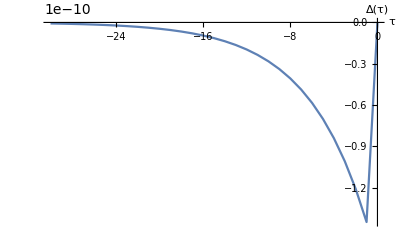

```mathematica
ListPlot[Table[lst[[31+i]]-lst[[31-i]],{i,30,0,-1}],DataRange->{-30,0},Joined->True,AxesLabel->{"τ","Δ(τ)"}]
```

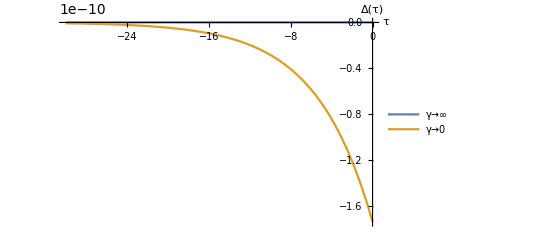

```mathematica
Plot[{fIDCtau[t]/.h->7,fDCtau[t]/.h->7},{t,-30,0},PlotRange->All,AxesLabel->{"τ","Δ(τ)"},PlotLegends->Placed[{"γ→∞","γ→0"},{0.1,0.8}]]
```

```mathematica
(*EQ degeneration*)
x1=1;
x2=1;
yLst={0,0,0,0,1,1,1,1};
mLst={0,1,0,1,0,1,0,1};
aLst={0,0,1,1,0,0,1,1};
fH[hh_,ii_]:=Exp[-hh*((x1-1/2)*(mLst[[ii]]-1/2)+(x2-1/2)*(aLst[[ii]]))];
matJump=Transpose[({{-(fH[h,1]*3), fH[h,1], fH[h,1], 0, fH[h,1], 0, 0, 0}, {fH[h,2], -(fH[h,2]*3), 0, fH[h,2], 0, fH[h,2], 0, 0}, {fH[h,3], 0, -(fH[h,3]*3), fH[h,3], 0, 0, fH[h,3], 0}, {0, fH[h,4], fH[h,4], -(fH[h,4]*3), 0, 0, 0, fH[h,4]}, {fH[h,5], 0, 0, 0, -(fH[h,5]*3), fH[h,5], fH[h,5], 0}, {0, fH[h,6], 0, 0, fH[h,6], -(fH[h,6]*3), 0, fH[h,6]}, {0, 0, fH[h,7], 0, fH[h,7], 0, -(fH[h,7]*3), fH[h,7]}, {0, 0, 0, fH[h,8], 0, fH[h,8], fH[h,8], -(fH[h,8])}})];
eigenVa=Eigenvalues[matJump];
eigenVeR=Eigenvectors[matJump];
eigenVeL=Eigenvectors[Transpose[matJump]];
```

```mathematica
xL={1,2,3,4,1,2,3,4};
yL={1,1,1,1,2,2,2,2};
matA=-TensorProduct[yL,xL]+TensorProduct[xL,yL];
matPA=TensorProduct[xL,yL];
matNA=TensorProduct[yL,xL];
(* Find NESS distributions*)
fWTilde[ww_]:=Join[ww[[1;;Dimensions[ww][[1]]-1]],{Table[1,Dimensions[ww][[2]]]}];
nessDist=Dot[Inverse[fWTilde[matJump]],Transpose[Table[0,Dimensions[fWTilde[matJump]][[2]]-1]~Join~{1}]];
xExp=xL.nessDist;
yExp=yL.nessDist;
fDCtau[t_]:=N[(Sum[Exp[-seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matA]],{i,8}])/(sxExp*syExp)];
fCtauP[t_]:=
N[(Sum[Exp[seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matPA]],{i,8}])/(sxExp*syExp)-1];
fCtauN[t_]:=N[(Sum[Exp[-seigenVa[[i]]*t]*Tr[Dot[TensorProduct[seigenVeR[[i]],nseigenVeL[[i]]*snessDist],matNA]],{i,8}])/(sxExp*syExp)-1];
```

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.h->7;
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
Rasterize[Plot[fDCtau[t],{t,-30,0},AxesLabel->{"τ","Δ(τ)"}]]
```

-Graphics-

```mathematica
lst=Table[fDCtau[i],{i,-30,0,0.5}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*Compare ana and sim*)
lst=Table[N[nessDist/.{h->7,g->i}],{i,0,20}];
```

```mathematica
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ana_h20.dat",lst]
```

F:\ThesisProject\RESULTS\01062023_testanasim\ana_h20.dat

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->13,h->13};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];maxima=Maximize[fCtauP[t],{t}∈Interval[{0.1,0.4}]];lst[[5,13]]={maxima[[1]],maxima[[2,1,2]]}
```

General::munfl: 1.3816×10^-193 (-5.49043×10^-206) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-0.00375097,0.4}

```mathematica
lstRatio=Table[lst[[i,j,1]]/lst[[i,j,2]],{i,5},{j,15}]
```

{{0.0867457,0.208418,0.393473,0.686122,1.15948,1.93368,3.20602,5.30114,8.75374,14.4451,23.828,39.2973,64.8017,106.856,176.14},{0.0106245,0.0242473,0.043896,0.0740866,0.122143,0.200043,0.327465,0.536805,0.881428,1.44927,2.38525,3.92826,6.47238,10.6639,17.5397},{0.000847066,0.00189389,0.00337684,0.00564405,0.00925494,0.0151192,0.0247248,0.0405127,0.0664982,0.1093,0.17983,0.296084,0.487779,0.803082,1.3256},{0.0000653776,0.000145312,0.000257906,0.000429647,0.000702941,0.00114671,0.00187373,0.0030695,0.00503892,0.00824791,0.013635,0.0224413,0.036977,0.0608623,0.10021},{5.24198×10^-6,0.0000116426,0.0000206624,0.0000343736,0.0000562117,0.0000916827,0.00014979,0.000245369,0.000402761,0.000662315,0.00108912,0.0017932,-0.00937742,0.0051461,0.00774487}}

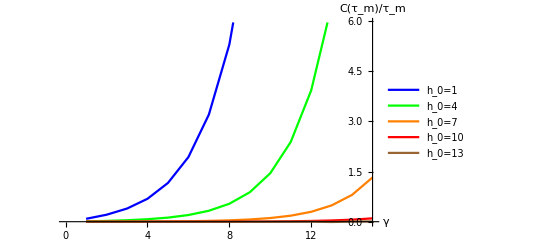

F:\ThesisProject\RESULTS\01062023_testanasim\ratio.png

```mathematica
ListLinePlot[lstRatio,AxesLabel->{"γ","C(τ_m)/τ_m"},PlotLegends->{"h_0=1","h_0=4","h_0=7","h_0=10","h_0=13"},PlotStyle->{Blue,Green,Orange,Red,Brown},AxesOrigin->{15,0}]
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ratio.png",%]
```

```mathematica
Rasterize[ListLinePlot[{lstRatio[[4,All]],lstRatio[[5,All]]},PlotStyle->{Red,Brown}]]
Export["F:\\ThesisProject\\RESULTS\\01062023_testanasim\\ratio_inset.png",%]
```

-Graphics-

F:\ThesisProject\RESULTS\01062023_testanasim\ratio_inset.png

```mathematica
(*Examine eigenvalue*)

lst=Table[0,4,61];
For[gg=0,gg<4,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->7,h->(2*gg+5)};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-30,0}]~Join~Table[fCtauP[i],{i,1,30}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},PlotRange->All,Joined->True]]
```

General::munfl: Exp[-3680.64] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3557.96] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3435.27] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Rasterize[ListPlot[lst[[2;;4,All]],PlotLegends->Table[i,{i,0,7}],DataRange->{-30,30},PlotRange->All,Joined->True]]
Export["F:\\ThesisProject\\RESULTS\\07062023_ana\\corr_hlines_2ip5.dat",lst]
```

-Graphics-

F:\ThesisProject\RESULTS\07062023_ana\corr_hlines_2ip5.dat

```mathematica
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];Print[N[seigenVa]];
Print[N[nseigenVeL]]]
```

```mathematica
(*08.06.2023 Expansion*)
Eigensystem[{{0,a,a,0},{1/a,0,0,a},{1/a,0,0,a},{0,1/a,1/a,0}}]
```

{{0,0,-2,2},{{-a^2,0,0,1},{0,-1,1,0},{a^2,-a,-a,1},{a^2,a,a,1}}}

```mathematica
Eigensystem[Transpose[{{0,a,a,0},{1/a,0,0,a},{1/a,0,0,a},{0,1/a,1/a,0}}]]
```

{{0,0,-2,2},{{-1/a^2,0,0,1},{0,-1,1,0},{1/a^2,-1/a,-1/a,1},{1/a^2,1/a,1/a,1}}}

```mathematica
eigenVa
```

{0,-2 ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),-ⅇ^(-h/2) (1+ⅇ^h),ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,1],ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,2],ⅇ^(-2-g-h/2) Root[2 ⅇ^(6+3 g+2 h)-2 ⅇ^(4+4 g+2 h)+(2 ⅇ^(4+2 g)+5 ⅇ^(4+2 g+h)-ⅇ^(2+3 g+h)+2 ⅇ^(4+2 g+2 h)) #1+(3 ⅇ^(2+g)+3 ⅇ^(2+g+h)) #1^2+#1^3&,3]}

```mathematica
nessDist//MatrixForm
```

LinearSolveFunction[…]

```mathematica
MatrixRank[matJump]
```

6

```mathematica
nessDist
```

{ⅇ^g/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+h)/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+h)/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(2 h)/((1+ⅇ^g) (1+ⅇ^h)^2),1/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^h/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^h/((1+ⅇ^g) (1+ⅇ^h)^2),ⅇ^(g+2 h)/((1+ⅇ^g) (1+ⅇ^h)^2)}

```mathematica
lst=Table[0,8,201];
For[gg=0,gg<8,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg+1]]=Table[fCtauN[i],{i,-10,0,0.1}]~Join~Table[fCtauP[i],{i,1,10,0.1}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,0,7}],DataRange->{-10,10},PlotRange->All,Joined->True]]
```

-Graphics-

```mathematica
Export["F:\\ThesisProject\\RESULTS\\08062023_expasion\\corr_zeroorder.png",%]
```

F:\ThesisProject\RESULTS\08062023_expasion\corr_zeroorder.png

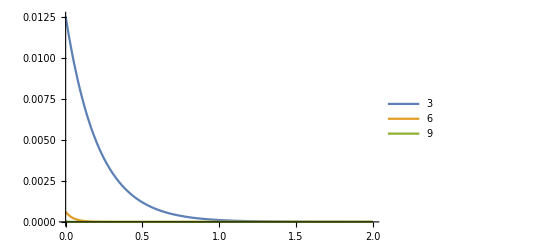

```mathematica
f0corr[g_,h_,t_]:=(E^(2 h-E^(-h/2) (1+E^h) t) (-1+E^g) (1+3 E^h+2 E^(2 h)))/((1+4 E^h) (1+E^(2 h)) (2+E^g+4 E^h+E^(2 h)+2 E^(g+h)+2 E^(g+2 h)));
Plot[{f0corr[7,3,t],f0corr[7,6,t],f0corr[7,9,t]},{t,0,2},PlotLegends->{3,6,9},PlotRange->All]
```

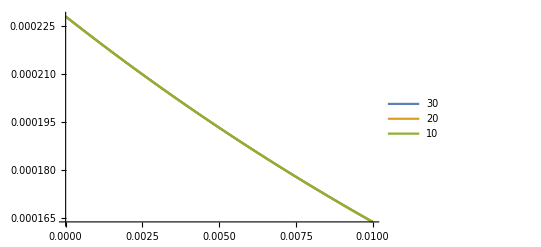

```mathematica
Plot[{fCtauP[t]/.{g->30,h->7},fCtauP[t]/.{g->20,h->7},fCtauP[t]/.{g->10,h->7}},{t,0,0.01},PlotRange->All,PlotLegends->{30,20,10}]
```

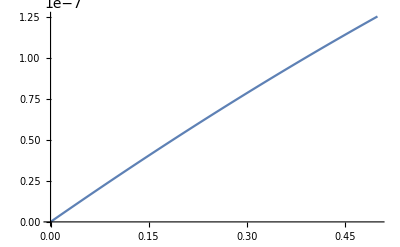

```mathematica
Plot[(Exp[x]-1)/(2*Exp[x+7]+2*Exp[x+14]+Exp[x]+4*Exp[7]+Exp[14]+2),{x,0,0.5}]
```

```mathematica
(*09.06.2023 Closer to corr*)
lst=Table[0,5,31];
For[gg=1,gg<=5,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg*2,h->7};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lst[[gg]]=Table[fCtauP[i],{i,0,6,0.2}]];
Rasterize[ListPlot[lst,PlotLegends->Table[i,{i,2,10,2}],DataRange->{0,6},PlotRange->All,Joined->True]]
```

General::munfl: Exp[-713.419] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-738.898] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-764.377] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
lstn=Table[0,15];
lstp=Table[0,15];
lstd=Table[0,15];
For[gg=1,gg<=15,gg++,{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->gg,h->7};nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];lstn[[gg]]=fCtauN[0];lstp[[gg]]=fCtauP[0];];
lstd=lstp-lstn
lstn
lstp
```

General::munfl: 9.16972×10^-152 (-4.11653×10^-160) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{6.93223×10^-13,8.96372×10^-12,2.02935×10^-11,1.33589×10^-11,-4.69624×10^-13,-2.18185×10^-11,1.44781×10^-8,-6.09801×10^-12,3.05054×10^-11,2.01195×10^-12,-1.53296×10^-10,-3.05682×10^-10,4.67217×10^-9,-2.94254×10^-8,1.32346×10^-8}

{0.00285236,0.00527807,0.0071108,0.00840853,0.00929614,0.00988645,0.0102691,0.010512,0.0106638,0.0107576,0.0108151,0.0108503,0.0108717,0.0108848,0.0108927}

{0.00285236,0.00527807,0.0071108,0.00840853,0.00929614,0.00988645,0.0102691,0.010512,0.0106638,0.0107576,0.0108151,0.0108503,0.0108717,0.0108847,0.0108927}

```mathematica
Export["F:\\ThesisProject\\RESULTS\\09062023_testonfeed\\diff_t0.dat",{lstd,lstp,lstn}]
```

F:\ThesisProject\RESULTS\09062023_testonfeed\diff_t0.dat

```mathematica
Rasterize[Plot[{conditionP[t,1,1],conditionP[t,1,2],conditionP[t,1,3],conditionP[t,1,4],conditionP[t,1,5],conditionP[t,1,6],conditionP[t,1,7],conditionP[t,1,8]},{t,0,10},PlotLegends->Placed[{"From (0,0,0)","From (1,0,0)","From (0,1,0)","From (1,1,0)", "From (0,0,1)","From (1,0,1)","From (0,1,1)","From (1,1,1)"},{0.8,0.4}],LabelStyle->7,AxesLabel->{"time","P(0,0,0)"},PlotRange->{-0.1,1.1}]]
Export["F:\\ThesisProject\\RESULTS\\22062023_complementary\\transient_eq_tos1.png",%]
```

-Graphics-

F:\ThesisProject\RESULTS\22062023_complementary\transient_eq_tos1.png

```mathematica
{seigenVa,seigenVeL,seigenVeR,snessDist,sxExp,syExp}={eigenVa,eigenVeL,eigenVeR,nessDist,xExp,yExp}/.{g->15,h->6};
nseigenVeL=Table[seigenVeL[[i]]/(seigenVeL[[i]].seigenVeR[[i]]),{i,1,8}];
Rasterize[Plot[{conditionP[t,8,1],conditionP[t,8,2],conditionP[t,8,3],conditionP[t,8,4],conditionP[t,8,5],conditionP[t,8,6],conditionP[t,8,7],conditionP[t,8,8]},{t,0,20},PlotLegends->Placed[{"From (0,0,0)","From (1,0,0)","From (0,1,0)","From (1,1,0)", "From (0,0,1)","From (1,0,1)","From (0,1,1)","From (1,1,1)"},{0.8,0.4}],LabelStyle->7,AxesLabel->{"time","P(1,1,1)"},PlotRange->{-0.1,1.1}]]
Export["F:\\ThesisProject\\RESULTS\\22062023_complementary\\transient_neq_tos8.png",%]
```

General::munfl: -7.25934×10^-151 (-2.69281×10^-158) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

F:\ThesisProject\RESULTS\22062023_complementary\transient_neq_tos8.png

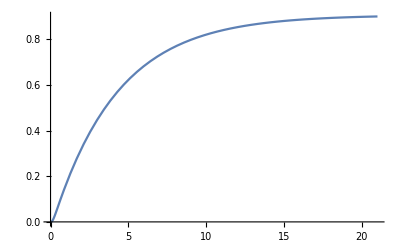

```mathematica
(*17.08.2023 Process correlation*)
Plot[tProp[8,1,t,0],{t,0,21}]
```

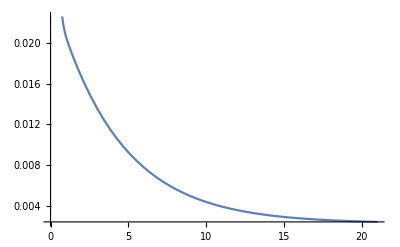

```mathematica
Plot[tProp[1,1,t,0],{t,0,21}]
```

```mathematica
eigenVeR[[2]]
```

{-8.55017×10^-15,0.5,-0.5,1.71774×10^-13,8.55213×10^-15,-0.5,0.5,-1.71856×10^-13}

```mathematica
eigenVeR[[0]]
```

List

```mathematica
eigenVeR[[2,2]]
```

0.5

```mathematica
propres=Table[Sum[Exp[eigenVa[[i]]*35]*eigenVeR[[i,j]]*eigenVeL[[i,1]],{i,1,8}],{j,1,8}]
```

General::munfl: Exp[-283922.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14135.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.00225448,0.0452546,0.0452546,0.00100466,2.06085×10^-9,0.0000249393,0.0000249393,0.906182}

```mathematica
eigenVeR[[8]]/propres
```

{1.09797,1.09804,1.09804,1.09801,1.09985,1.1008,1.1008,1.1008}

General::munfl: Exp[-283922.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14135.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

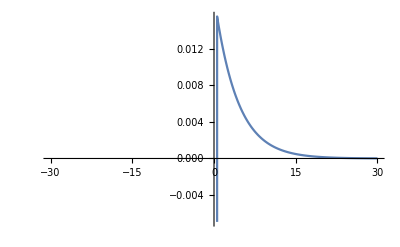

```mathematica
Plot[fCtauP[tau,35,initstate],{tau,-30,30}]
```

General::munfl: Exp[-283922.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14135.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

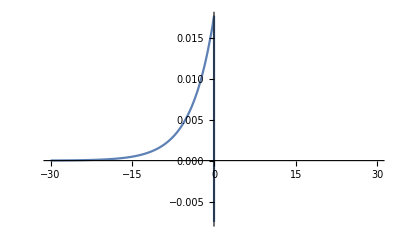

```mathematica
Plot[fCtauN[tau,35,initstate],{tau,-30,30}]
```

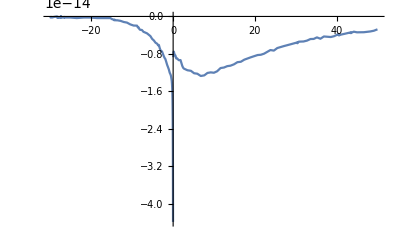
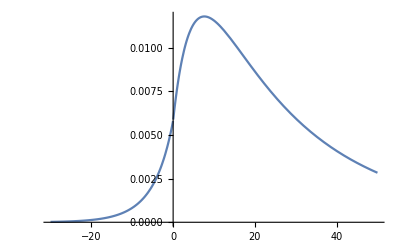
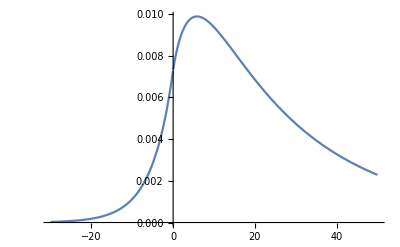
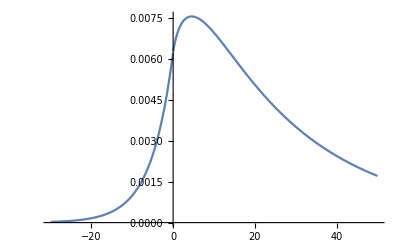
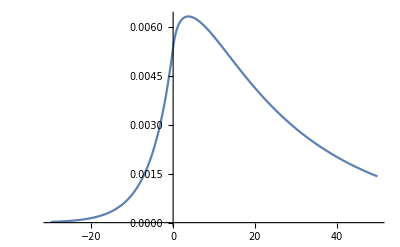
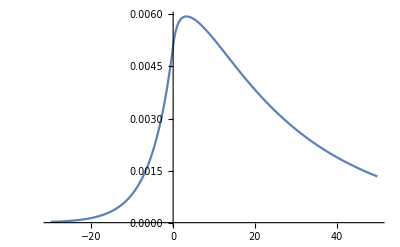
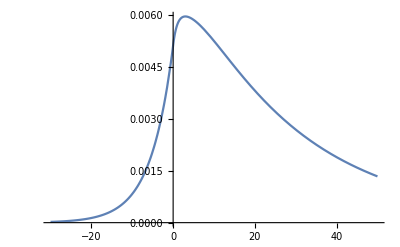
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}[3]

```mathematica
corrtimelst[3]
```

```mathematica
Table[fCtau[tau,t,initstate],{t,0,30,5}]
```

General::munfl: Exp[-772.739] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{Piecewise[{{1, tau<0}, {-2.39808×10^-14 (1.1986×10^-6 ⅇ^(-38.6369 tau)+6.43406×10^-7 ⅇ^(-11.6856 tau)-1.58717×10^-34 ⅇ^(-1.16512 tau)-0.0000419575 ⅇ^(-1.11344 tau)-3.08048×10^-33 ⅇ^(-0.347548 tau)-0.0000418355 ⅇ^(-0.181643 tau)+0.0000145522 ⅇ^(-0.0334946 tau)+0.0000673988 ⅇ^(1.4366×10^-16 tau))+96, tau≥0}, {0, True}}],Piecewise[{{0.000635947 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+65, tau<0}, {0.459986 (1.1986×10^-6 ⅇ^(-38.6369 tau)+10+0.0000673988 ⅇ^(1.4366×10^-16 tau))+65, tau≥0}, {0, True}}],Piecewise[{{0.000311699 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+65, tau<0}, {1.0775 (1.1986×10^-6 ⅇ^(-38.6369 tau)+9+1+0.0000673988 ⅇ^(1.4366×10^-16 3))+65, tau≥0}, {0, True}}],Piecewise[{{0.000184658 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+0.000553974 (1)+64, tau<0}, {1.68396 (1.1986×10^-6 ⅇ^(-38.6369 tau)+10+0.0000673988 ⅇ^1)+65, tau≥0}, {0, True}}],Piecewise[{{0.00013674 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+65, tau<0}, {2.23081 (1.1986×10^-6 ⅇ^(-38.6369 tau)+9+24 1+0.0000673988 ⅇ^(24 tau))+65, tau≥0}, {0, True}}],Piecewise[{{0.000120219 (0.000791808 ⅇ^(-1.4366×10^-16 tau)+0.0000318128 ⅇ^(0.0334946 tau)+0.0137679 ⅇ^(0.181643 tau)+1.40694×10^-32 ⅇ^(0.347548 tau)-0.0013527 ⅇ^(1.11344 tau)+6.7036×10^-34 ⅇ^(1.16512 tau)+0.93798 ⅇ^(11.6856 tau)-0.951219 ⅇ^(38.6369 tau))+65, tau<0}, {2.70702 (1.1986×10^-6 ⅇ^(-38.6369 tau)+10+0.0000673988 ⅇ^(1.4366×10^-16 tau))+65, tau≥0}, {0, True}}],{ | 1}
 |  |  |  |

```mathematica
Plot[{fCtau[tau,0,initstate],fCtau[tau,5,initstate],fCtau[tau,10,initstate],fCtau[tau,15,initstate],fCtau[tau,20,initstate],fCtau[tau,25,initstate],fCtau[tau,30,initstate]},{tau,-30,50},PlotLegends->Table[t,{t,0,30,5}]]
```

```mathematica
samplingpoints=Table[Table[fCtau[tau,t,initstate],{tau,-50,50,0.25}],{t,0,25,5}]
```

General::munfl: Exp[-1931.85] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
skews=Table[Skewness[samplingpoints[[i]]],{i,1,6}]
```

{-1.3491,0.44425,0.420943,0.439751,0.465607,0.487254}

```mathematica
Skewness[{1,2,4,5,6}]
Skewness[2*{1,2,4,5,6}]
```

-63/(43 √86)

-63/(43 √86)

```mathematica
Skewness[{0,0,0,1,1,1}]
```

0

```mathematica
Kurtosis[{1,2,3,4,5}]
```

17/10

```mathematica
Kurtosis[2*{1,2,3,4,5}]
```

17/10

```mathematica
Kurtosis[{1,1.5,2,2.5,3}]
```

1.7

```mathematica
Kurtosis[{0,0,0,1,1,1}]
```

1

```mathematica
Kurtosis[{1,1,1}]
```

Indeterminate

```mathematica
Kurtosis[{0,1,1,1,0}]
```

7/6

```mathematica
Skewness[{0.1,0.1,0.1,1,1,1}]
```

3.55353×10^-16

```mathematica
Skewness[{0.9,0.9,0.9,1.1,1.1,1.1}]
```

1.59016×10^-15

```mathematica
Skewness[{0.1,0.1,0.1,1.1,1.1,1.1}]
```

3.33067×10^-16

```mathematica
Kurtosis[{0.9,0.9,0.9,1.1,1.1,1.1}]
Kurtosis[{0.1,0.1,0.1,1.1,1.1,1.1}]
```

1.

1.

```mathematica
Integrate[fDCtau[tau,1,6],{tau,0,2}]/Integrate[fPCtau[tau,1,6],{tau,0,2}]
```

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

```mathematica
Integrate[fDCtau[tau,1,6],{tau,0,2}]
```

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.168084

```mathematica
Integrate[fPCtau[tau,1,6],{tau,0,2}]
```

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.

```mathematica
NIntegrate[fCtauP[tau,1,6],{tau,0,5}]
NIntegrate[fCtauN[tau,1,6],{tau,0,5}]
```

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.778535

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-1.59893056851998×10^1857

```mathematica
fCtauP[0,1,6]
fCtauP[1,1,6]
```

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0853159

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.163762

```mathematica
NIntegrate[fPCtau[tau,1,initstate],{tau,0,2}]
```

General::munfl: Exp[-865.609] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.44556

General::munfl: Exp[-9.78395×10^10] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.87114×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

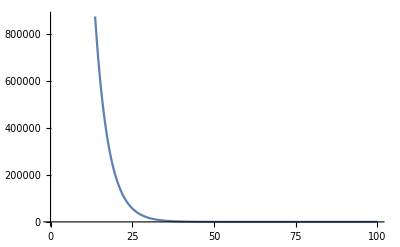

```mathematica
Plot[tProp[8,3,t,0],{t,0,100}]
```

```mathematica
isample={0,0.02,0.04,0.06,0.08,0.1,0.2,0.3,0.4,0.5,0.6,1,3,5,7,9,11,16,21,26};

ini1=ReadList["F:\\ThesisProject\\RESULTS\\12092023_asymmetry_eq\\g15h7tau20_00_1.dat",Number];

ini2=ReadList["F:\\ThesisProject\\RESULTS\\12092023_asymmetry_eq\\g15h7tau20_00_2.dat",Number];

ini4=ReadList["F:\\ThesisProject\\RESULTS\\12092023_asymmetry_eq\\g15h7tau20_00_4.dat",Number];

ini5=ReadList["F:\\ThesisProject\\RESULTS\\12092023_asymmetry_eq\\g15h7tau20_00_5.dat",Number];
ini6=ReadList["F:\\ThesisProject\\RESULTS\\12092023_asymmetry_eq\\g15h7tau20_00_6.dat",Number];
ini8=ReadList["F:\\ThesisProject\\RESULTS\\12092023_asymmetry_eq\\g15h7tau20_00_8.dat",Number];
```

```mathematica
ini1data=Transpose[{isample,ini1}];
ini2data=Transpose[{isample,ini2}];
ini4data=Transpose[{isample,ini4}];
ini5data=Transpose[{isample,ini5}];
ini6data=Transpose[{isample,ini6}];
ini8data=Transpose[{isample,ini8}];
```

```mathematica
Rasterize[ListLogLinearPlot[{ini1data,ini2data,ini4data,ini5data,ini6data,ini8data},PlotLegends->{"ini:(0m,0a,0y)","ini:(1m,0a,0y)","ini:(1m,1a,0y)","ini:(0m,0a,1y)","ini:(1m,0a,1y)","ini:(1m,1a,1y)"},Joined->True,PlotRange->Automatic]]
```

-Graphics-

```mathematica
Rasterize[ListLogLinearPlot[{ini2data,ini5data,ini6data,ini8data},PlotLegends->{"ini:(1m,0a,0y)","ini:(0m,0a,1y)","ini:(1m,0a,1y)","ini:(1m,1a,1y)"},Joined->True,PlotRange->Full]]
```

-Graphics-

```mathematica
nessDist
```

{0.907397,0.0451517,0.0451517,2.48457×10^-6,8.30887×10^-7,0.0000249451,0.0000249451,0.00224673}

```mathematica
Sum[nessDist[[i]],{i,1,8}]
```

1.

```mathematica
fDist[0,nessDist]
```

{0.907397,0.0451517,0.0451517,2.48457×10^-6,8.30887×10^-7,0.0000249451,0.0000249451,0.00224673}

```mathematica
fDist[3,nessDist]
```

General::munfl: Exp[-24336.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1211.63] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1211.62] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.0135116,0.265325,0.265325,0.00594758,4.81353×10^-9,0.0000124477,0.0000124477,0.449866}

```mathematica
Sum[%[[i]],{i,1,8}]
```

1.

```mathematica
fsDist[5,nessDist]
```

General::munfl: Exp[-40560.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2019.38] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2019.37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.00922124,0.18145,0.18145,0.0040637,3.76441×10^-9,0.0000172086,0.0000172086,0.62378}

```mathematica
fsDist[20,nessDist]
```

General::munfl: Exp[-162241.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8077.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.00244033,0.048888,0.048888,0.00108627,2.1063×10^-9,0.0000247331,0.0000247331,0.898648}

General::munfl: Exp[-121681.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6058.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6058.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

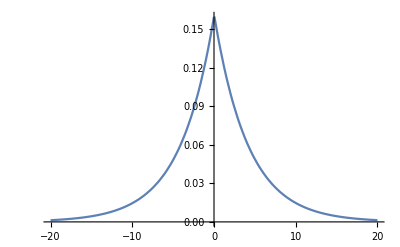

```mathematica
Plot[fsCtau[tau,15,nessDist],{tau,-20,20},Evaluated->True]
```

```mathematica
fsCtau[10,15,nessDist]
```

General::munfl: Exp[-121681.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6058.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6058.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0147112

```mathematica
fsAsym[10,nessDist]//Timing
fAsym[10,6]//Timing
```

General::munfl: Exp[-81120.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4038.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.14063,0.138831}

General::munfl: Exp[-81120.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4038.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.046875,0.299471}

```mathematica
fH[gg_,hh_,ii_]:=Exp[-hh*((x1-1/2)*(mLst[[ii]]-1/2)+(x2-1/2)*(aLst[[ii]]-1/2))+gg/2*(yLst[[ii]]-mLst[[ii]]*aLst[[ii]])^2];
matJump=Transpose[({{-(fH[g,h,1]*3), fH[g,h,1], fH[g,h,1], 0, fH[g,h,1], 0, 0, 0}, {fH[g,h,2], -(fH[g,h,2]*3), 0, fH[g,h,2], 0, fH[g,h,2], 0, 0}, {fH[g,h,3], 0, -(fH[g,h,3]*3), fH[g,h,3], 0, 0, fH[g,h,3], 0}, {0, fH[g,h,4], fH[g,h,4], -(fH[g,h,4]*3), 0, 0, 0, fH[g,h,4]}, {fH[g,h,5], 0, 0, 0, -(fH[g,h,5]*3), fH[g,h,5], fH[g,h,5], 0}, {0, fH[g,h,6], 0, 0, fH[g,h,6], -(fH[g,h,6]*3), 0, fH[g,h,6]}, {0, 0, fH[g,h,7], 0, fH[g,h,7], 0, -(fH[g,h,7]*3), fH[g,h,7]}, {0, 0, 0, fH[g,h,8], 0, fH[g,h,8], fH[g,h,8], -(fH[g,h,8]*3)}})];
```

General::munfl: Exp[-6.51553×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.276×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.46596×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

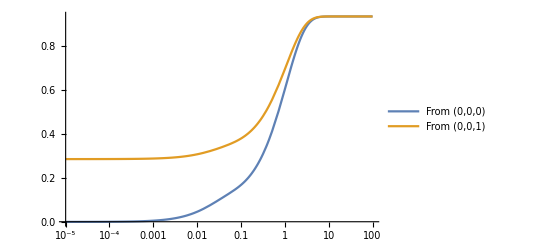

{1.11022×10^-16,-6.93889×10^-17,0.,-6.31089×10^-29,1.,-1.3659×10^-17,-5.27784×10^-17,-0.000583593}

ReplaceAll::reps: {{c[1]→-1.14779,c[2]→-0.303642,c[3]→0.689086,c[4]→2.3255×10^-13,c[5]→0.492652,c[6]→-0.0235453,c[7]→0.741874}==0.25} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(c[1]→-1.14779)==0.25&&(c[2]→-0.303642)==0.25&&(c[3]→0.689086)==0.25&&(c[4]→2.3255×10^-13)==0.25&&(c[5]→0.492652)==0.25&&(c[6]→-0.0235453)==0.25&&(c[7]→0.741874)==0.25} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NSolve[0.934429-0.00979178 ⅇ^(-6.51339×10^14 t) c[1]-2.94511×10^-16 ⅇ^(-4.27459×10^13 t) c[2]-0.430938 ⅇ^(-2.46515×10^13 t) c[3]+0.288675 ⅇ^(-1.59614×10^12 t) c[4]-0.0805863 ⅇ^(-52.6827 t) c[5]-0.000207936 ⅇ^(-2.74925 t) c[6]-0.821705 ⅇ^(-0.931707 t) c[7]/.{c[1]→-1.14779,c[2]→-0.303642,c[3]→0.689086,c[4]→2.3255×10^-13,c[5]→0.492652,c[6]→-0.0235453,c[7]→0.741874}==0.25,t]

```mathematica
LogLinearPlot[{(pss[[8]]+Sum[evec[[j]][[8]] c[j]Exp[λvec[[j]] t],{j,1,7}])/.csub1,pss[[8]]+Sum[evec[[j]][[8]] c[j]Exp[λvec[[j]] t],{j,1,7}]/.csub2},{t,10^-5,100},PlotRange->All,PlotLegends->{"From (0,0,0)","From (0,0,1)"}]
pss+Sum[evec[[j]] c[j],{j,1,7}]/.csub2
NSolve[pss[[8]]+Sum[evec[[j]][[8]] c[j]Exp[λvec[[j]] t],{j,1,7}]/.csub2==0.25,t]
```

```mathematica
pss[[8]]+Sum[evec[[j]][[8]] c[j]Exp[λvec[[j]] 10^(-14)],{j,1,7}]/.csub2
```

0.0530726

```mathematica
Cases[Table[i,{i,1,7}],Except[measureState]]
```

{2,3,4,5,6,7}

```mathematica
csub1=Flatten[NSolve[Flatten[Join[{pss[[5-measureState]]+Sum[evec[[j]][[5-measureState]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,zeroterms}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]
cNeq1=Flatten[NSolve[Flatten[Join[{pssNeq[[5-measureState]]+Sum[evecNeq[[j]][[5-measureState]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,zeroterms}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]
```

{c[1]→1.1547,c[2]→2.25736×10^-17,c[3]→6.15631×10^-17,c[4]→-4.62557×10^-14,c[5]→0.000485289,c[6]→0.000147477,c[7]→-0.11984}

{c[1]→-1.41421-1.87615×10^-26 c[7],c[2]→3.41333×10^-13-2.54456×10^-12 c[7],c[3]→2.4241×10^-13-1.80711×10^-12 c[7],c[4]→4.84992×10^-25-3.53106×10^-24 c[7],c[5]→-0.124569+0.926093 c[7],c[6]→0.0318579+0.0523585 c[7]}

```mathematica
csub1=Flatten[NSolve[Flatten[Join[{pss[[measureState]]+Sum[evec[[j]][[measureState]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,zeroterms}]}]],Table[c[j],{j,1,7}]]]
cNeq1=Flatten[NSolve[Flatten[Join[{pssNeq[[measureState]]+Sum[evecNeq[[j]][[measureState]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,zeroterms}]}]],Table[c[j],{j,1,7}]]]
```

{c[1]→-6.03704×10^-17,c[2]→-1.1408×10^-15,c[3]→-1.1427×10^-15,c[4]→-5.7×10^-14,c[5]→-0.00147112,c[6]→-0.0000264134,c[7]→-0.117935}

{c[1]→-1.54297×10^-26,c[2]→-1.30204×10^-16,c[3]→-9.24695×10^-17,c[4]→6.66083×10^-19,c[5]→-0.00029287,c[6]→0.038884,c[7]→0.134194}

```mathematica
csub1=Flatten[NSolve[Flatten[Join[{pss[[1]]+Sum[evec[[j]][[1]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]
cNeq1=Flatten[NSolve[Flatten[Join[{pssNeq[[1]]+Sum[evecNeq[[j]][[1]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]
```

{c[1]→-6.03704×10^-17,c[2]→-1.1408×10^-15,c[3]→-1.1427×10^-15,c[4]→-5.7×10^-14,c[5]→-0.00147112,c[6]→-0.0000264134,c[7]→-0.117935}

{c[1]→-1.54297×10^-26,c[2]→-1.30204×10^-16,c[3]→-9.24695×10^-17,c[4]→6.66083×10^-19,c[5]→-0.00029287,c[6]→0.038884,c[7]→0.134194}

```mathematica
csub2=Flatten[NSolve[Flatten[Join[{pss[[5]]+Sum[evec[[j]][[5]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,1,4}],Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,6,7}]}]],Table[c[j],{j,1,7}]]]
cNeq2=Flatten[NSolve[Flatten[Join[{pssNeq[[5]]+Sum[evecNeq[[j]][[5]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,1,4}],Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,6,7}]}]],Table[c[j],{j,1,7}]]]
```

```mathematica
csub2=If[measureState!=1,Flatten[NSolve[Flatten[Join[{pss[[9-measureState]]+Sum[evec[[j]][[9-measureState]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,zeroterms}]}]],Table[c[j],{j,1,7}]]],Flatten[NSolve[Flatten[Join[{pss[[8]]+Sum[evec[[j]][[8]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]]
cNeq2=If[measureState!=1,Flatten[NSolve[Flatten[Join[{pssNeq[[9-measureState]]+Sum[evecNeq[[j]][[9-measureState]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,zeroterms}]}]],Table[c[j],{j,1,7}]]],Flatten[NSolve[Flatten[Join[{pssNeq[[8]]+Sum[evecNeq[[j]][[8]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]]
```

{}

{}

```mathematica
zeroterms
```

{1,2,3,4,6,7}